```mathematica
<<SimulationTools`
```

## Exact plane wave solution

```mathematica
ClearAll[omega,nx,ny,nz,nt,w];
omega[wavenumber_]:=Sqrt[Sum[wavenumber⟦i⟧^2,{i,1,3}]];
nx[wavenumber_,spaceoffset_,x_]:=wavenumber⟦1⟧*(x-spaceoffset⟦1⟧);
ny[wavenumber_,spaceoffset_,y_]:=wavenumber⟦2⟧*(y-spaceoffset⟦2⟧);
nz[wavenumber_,spaceoffset_,z_]:=wavenumber⟦3⟧*(z-spaceoffset⟦3⟧);
nt[wavenumber_,timeoffset_,t_]:=omega[wavenumber]*(t-timeoffset);
w[wavenumber_,spaceoffset_,timeoffset_,t_,x_,y_,z_]:=2π(nx[wavenumber,spaceoffset,x]+ny[wavenumber,spaceoffset,y]+nz[wavenumber,spaceoffset,z]+nt[wavenumber,timeoffset,t]);

ClearAll[Phi,KPhi];
Phi[wavenumber_,spaceoffset_,timeoffset_,t_,x_,y_,z_]:=Cos[w[wavenumber,spaceoffset,timeoffset,t,x,y,z]]
KPhi[wavenumber_,spaceoffset_,timeoffset_,t_,x_,y_,z_]:=-1/2D[Phi[wavenumber,spaceoffset,timeoffset,tt,x,y,z],tt]//.tt->t;

ClearAll[PhiRHS,KPhiRHS];
PhiRHS[wavenumber_,spaceoffset_,timeoffset_,t_,x_,y_,z_]:=-2KPhi[wavenumber,spaceoffset,timeoffset,t,x,y,z];
KPhiRHS[wavenumber_,spaceoffset_,timeoffset_,t_,x_,y_,z_]:=-1/2Laplacian[Phi[wavenumber,spaceoffset,timeoffset,t,xx,yy,zz],{xx,yy,zz}]//.{xx->x,yy->y,zz->z};
```

## Invariants

```mathematica
ClearAll[map,function];
map=0;
function="K_Phi_rhs";

ClearAll[xyPlane,xLine];
xyPlane=0;
xLine={0,0};

ClearAll[dirs];
dirs={
NotebookDirectory[]<>"Test_Multipatch_coarse",
NotebookDirectory[]<>"Test_Multipatch_medium",
NotebookDirectory[]<>"Test_Multipatch_fine",
NotebookDirectory[]<>"Test_Multipatch_finer"
};
```

## Error plot

```mathematica
ClearAll[plots];
plots={};

ClearAll[i];
For[i=1,i≤Length[dirs],i++,
ClearAll[dir];
dir=dirs⟦i⟧;

ClearAll[sim3DGF,sim2DGF,sim1DGF];
sim3DGF=ReadGridFunction[dir,function,"xyz",Iteration->0,Map->map];
sim2DGF=Slab[sim3DGF,All,All,xyPlane];
sim1DGF=Slab[sim2DGF,All,xLine⟦1⟧,xLine⟦2⟧];

ClearAll[minx,maxx,points,analyticSolutionData];
minx=MinCoordinates[sim1DGF]⟦1⟧;
maxx=MaxCoordinates[sim1DGF]⟦1⟧;
points=Dimensions[sim1DGF]⟦1⟧-1;
dx=(maxx-minx)/points;
analyticSolutionData=ToDataRegion[Table[KPhiRHS[{1,1,1},{0,0,0},0,0,x,0,0],{x,minx,maxx,dx}],{minx},{dx}];

AppendTo[plots,
GraphicsRow[
{
ArrayPlot[sim2DGF,ColorFunction->"TemperatureMap",PlotRange->{Full,Full,Full},FrameTicks->Automatic,FrameLabel->{"x","y"},PlotLabel->function],
ListPlot[sim1DGF,Axes->False,Frame->True,PlotRange->{Full,Full},FrameLabel->{"x",function},PlotLabel->function<>" {y,z} = "<>ToString[xLine] ],
ListPlot[analyticSolutionData,Axes->False,Frame->True,PlotRange->{Full,Full},FrameLabel->{"x",function},PlotLabel->function<>" analytic"],
ListPlot[Abs[sim1DGF-analyticSolutionData]⟦3;;-3⟧,Axes->False,Frame->True,PlotRange->{Full,Full},FrameLabel->{"x",function<>" error"},PlotLabel->function<>" error"]
}
]
];

ClearAll[dir];
ClearAll[maps,iterations,refinamentLevels];
ClearAll[sim3DGF,sim2DGF,sim1DGF];
ClearAll[minx,maxx,points,analyticSolutionData];
]
ClearAll[i];

GraphicsColumn[plots,ImageSize->1.2*10^3]
```

-Graphics-

## Convergence plot

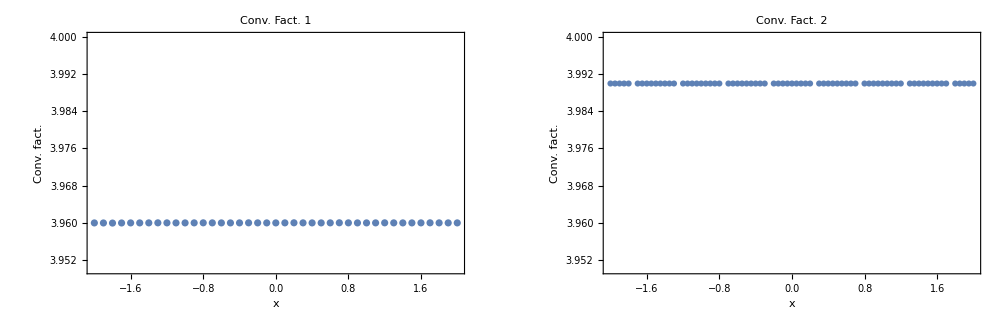

```mathematica
ClearAll[gfs];
gfs={};

ClearAll[i];
For[i=1,i≤Length[dirs],i++,
ClearAll[dir];
dir=dirs⟦i⟧;

ClearAll[sim3DGF,sim2DGF,sim1DGF];
sim3DGF=ReadGridFunction[dir,function,"xyz",Iteration->0,Map->map];
sim2DGF=Slab[sim3DGF,All,All,xyPlane];
sim1DGF=Slab[sim2DGF,All,xLine⟦1⟧,xLine⟦2⟧];

AppendTo[gfs,sim1DGF];

ClearAll[dir];
ClearAll[sim3DGF,sim2DGF,sim1DGF];
]
ClearAll[i];

GraphicsRow[
{
ListPlot[Log[WithResampling[(gfs⟦1⟧-gfs⟦2⟧)/(gfs⟦2⟧-gfs⟦3⟧)]]/Log[2],Axes->False,Frame->True,PlotRange->{Full,{3.95,4}},FrameLabel->{"x","Conv. fact."},PlotLabel->"Conv. Fact. 1" ],

ListPlot[Log[WithResampling[(gfs⟦2⟧-gfs⟦3⟧)/(gfs⟦3⟧-gfs⟦4⟧)]]/Log[2],Axes->False,Frame->True,PlotRange->{Full,{3.95,4}},FrameLabel->{"x","Conv. fact."},PlotLabel->"Conv. Fact. 2" ]
},
ImageSize->10^3
]
```